# Plots for my Master thesis

This notebook contains all settings and specifications for the plots I created in the scope of my Master thesis entitled “Quark Spectral Functions from Dyson-Schwinger Equations via Spectral Renormalization”.

## Initialization and Settings

```mathematica
SetDirectory[NotebookDirectory[]<>"data"];
					
SetOptions[$FrontEndSession,NotebookAutoSave -> True]
NotebookSave[]
<<NumericalCalculus`
```

```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"] (*easier tick specifications*)
```

```mathematica
exportPath=FileNameJoin[{NotebookDirectory[],"plots"}]; (*specify where plots are saved*)
```

```mathematica
SetAttributes[exportFigure,HoldFirst]
exportFigure[figure_]:=Export[FileNameJoin[{exportPath,StringJoin[ToString[SymbolName[Unevaluated@figure]],".pdf"]}],figure]; (*Plots should be safed as PDF*)
```

### Color Selection

Defining the same colors as used in the LaTeX document. Note that RGBColor only takes values between 0 and 1, therefore we have to rescale the original numbers.

```mathematica
MScRed = RGBColor[157/255,0,0]
MScBlue = RGBColor[1/255,1/255,141/255]
MScGreen = RGBColor[0,119/255,85/255]
MScGray = RGBColor[102/255, 102/255, 142/255]
```

RGBColor[Rational[157, 255], 0, 0]

RGBColor[Rational[1, 255], Rational[1, 255], Rational[47, 85]]

RGBColor[0, Rational[7, 15], Rational[1, 3]]

RGBColor[Rational[2, 5], Rational[2, 5], Rational[142, 255]]

```mathematica
MScColors = {MScBlue,MScRed, MScGreen}
```

{RGBColor[Rational[1, 255], Rational[1, 255], Rational[47, 85]],RGBColor[Rational[157, 255], 0, 0],RGBColor[0, Rational[7, 15], Rational[1, 3]]}

### Font Selection

We want to label our plots with the same font as used in the tex-document (“Palatino”)

```mathematica
MScFont = {FontFamily->"Palatino",FontSize->40}
```

{FontFamily→Palatino,FontSize→40}

### Watermark for preliminary Results

```mathematica
watermark = Style["Preliminary", 52, Bold, Opacity[.3]]
```

Preliminary

### Settings for larger tick markers

```mathematica
SetOptions[LinTicks,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}];
SetOptions[LogTicks,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}];
```

## Gluon Propagator + Spectral Function

```mathematica
GluonProp[p_,rescaling_ :52/100]:=rescaling*(2.6593023336775623 (0.24101744007732523 p^2-1.3080381149734166 p^4+0.4540243805575766 √(p^2)+3.102572099727779 (p^2)^(3/2)+0.6370104930721061 (p^2)^(5/2)) (1/(0.7223337923370855+(0.10014054778030819+p)^2))^1.940947667539462 (1/(0.7223006948918959+(0.10016935623821763+p)^2))^1.6111555266576754 (1/(5.603766404618137+(1.1510177570696811+p)^2))^0.2962151724379364 (1/(12.971529659828924+(1.220130041357888+p)^2))^0.168591834497177 (1/(5.9553300841709165+(1.5564010970324915+p)^2))^1.8976530064403432)/((p^2)^0.1425720117966328 (1/(6.359002348225766+(2.364448929855074+p)^2))^2.545863533505827 Log[1+0.32634744468212906 p^2]^0.22278738808344056)
```

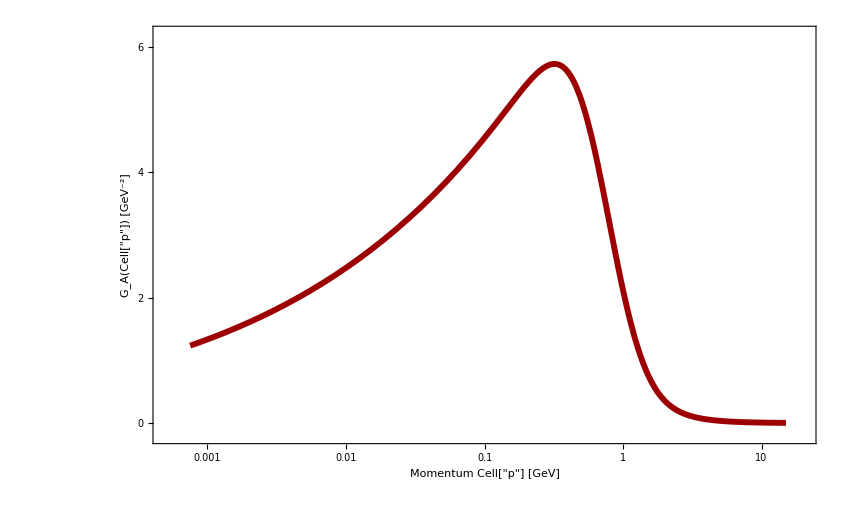

```mathematica
GluonPropPlot=LogLinearPlot[GluonProp[p],{p,0.75*10^-3,1.5*10^1},
ImageSize->850,Frame->True,Exclusions->None,Axes->None,
PlotRange->{xRange={0.5*10^-3, 2*10^1},yRange={-0.2,6.2}},
PlotStyle->{Directive[MScRed,Thickness[0.005]]}, 
FrameStyle->Directive[Black,Thickness[0.005]],
LabelStyle->MScFont,
FrameLabel->{"Momentum Cell["p",ExpressionUUID->"ebc16d0c-1826-41ec-901b-5c51bef40419"] [GeV]", "G_A(Cell["p",ExpressionUUID->"95aace13-849e-48e5-b1bb-584171f38b78"]) [GeV^-2]"},
FrameTicks->{{LinTicks[Sequence@@yRange, ShowMinorTicks->False,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[Sequence@@xRange,ShowMinorTicks->True,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True,LogPlot->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}}(*,
Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
]
exportFigure[GluonPropPlot];
```

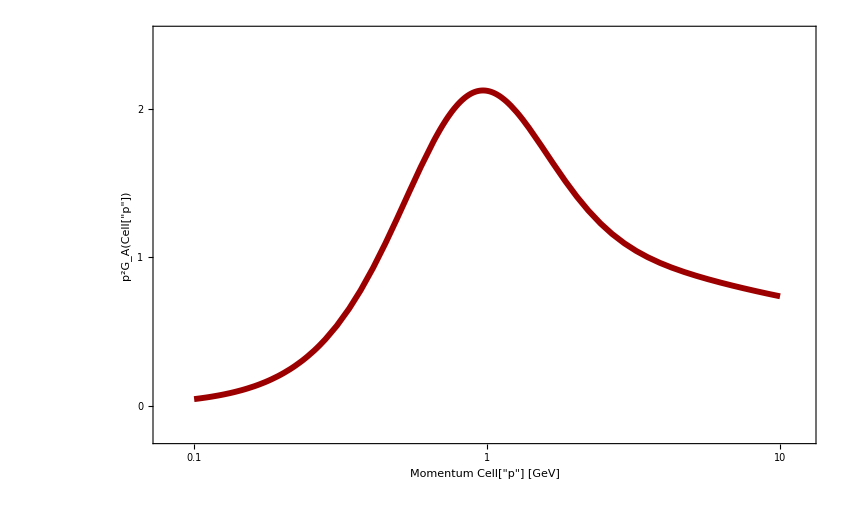

```mathematica
GluonPropDressingPlot=LogLinearPlot[p^2*GluonProp[p],{p,10^-1,10^1},
ImageSize->850,Frame->True,Exclusions->None,Axes->None,
PlotRange->{xRange={0.8*10^-1, 1.2*10^1},yRange={-0.2,2.5}},
PlotStyle->{Directive[MScRed,Thickness[0.005]]}, 
FrameStyle->Directive[Black,Thickness[0.005]],
LabelStyle->MScFont,
FrameLabel->{"Momentum Cell["p",ExpressionUUID->"d8775f00-2415-4e94-b011-022b71c51dd6"] [GeV]", "p^2G_A(Cell["p",ExpressionUUID->"15321155-62a3-4133-8bb8-57da5525d635"])"},
FrameTicks->{{LinTicks[Sequence@@yRange, ShowMinorTicks->False,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[Sequence@@xRange,ShowMinorTicks->True,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True,LogPlot->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}}(*,
Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
]
exportFigure[GluonPropDressingPlot];
```

```mathematica
GluonSpecFunc[ω_,ε_ :5*10^-8, rescaling_ : 52/100]:=-2Im[GluonProp[I*ω+ε, rescaling]]
```

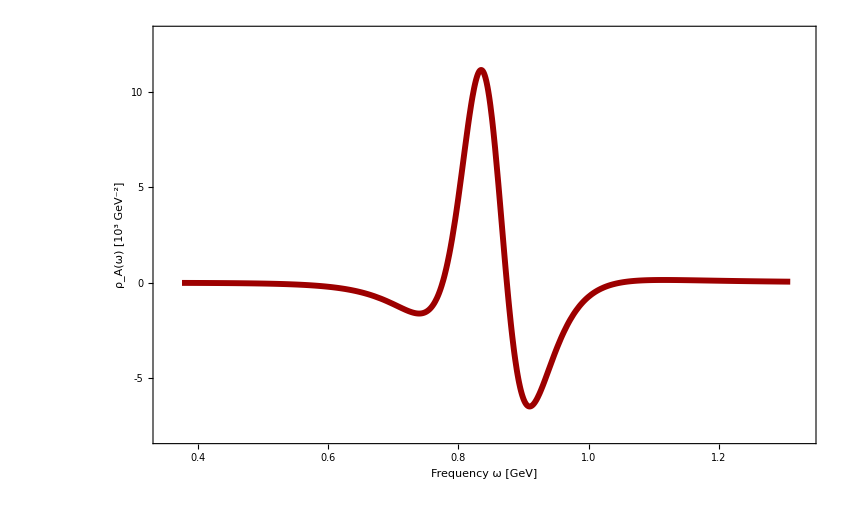

```mathematica
GluonSpecFuncPlot=Plot[GluonSpecFunc[ω],{ω,0.375,1.31},
ImageSize->850,Frame->True,Exclusions->None,Axes->None,
PlotRange->{xRange={0.35,1.33},yRange={-8000,13000}},
PlotStyle->{Directive[MScRed,Thickness[0.005]]}, 
FrameStyle->Directive[Black,Thickness[0.005]],
LabelStyle->MScFont,
FrameLabel->{"Frequency ω [GeV]", "  ρ_A(ω) [10^3 GeV^-2]"},
FrameTicks->{{LinTicks[Sequence@@yRange, TickLabelFunction->(IntegerPart[#/10^3 ]&), ShowMinorTicks->False,TickLabelStep->1],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LinTicks[Sequence@@xRange,ShowMinorTicks->True],LinTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}}(*,
Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
]
exportFigure[GluonSpecFuncPlot];
```

## Quark Spectral Functions

```mathematica
<<"realtime_quark_specfuncs_first_trials.mx"
```

```mathematica
Interpolation[quarkSEVecItersE[[1]]]
```

InterpolatingFunction[…]

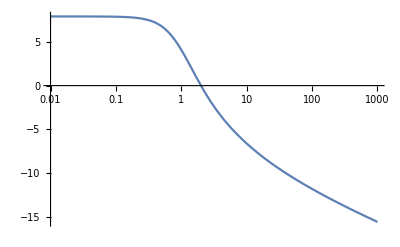

```mathematica
LogLinearPlot[%1231[x],{x,0.01,1000.}]
```

### Dressings Functions

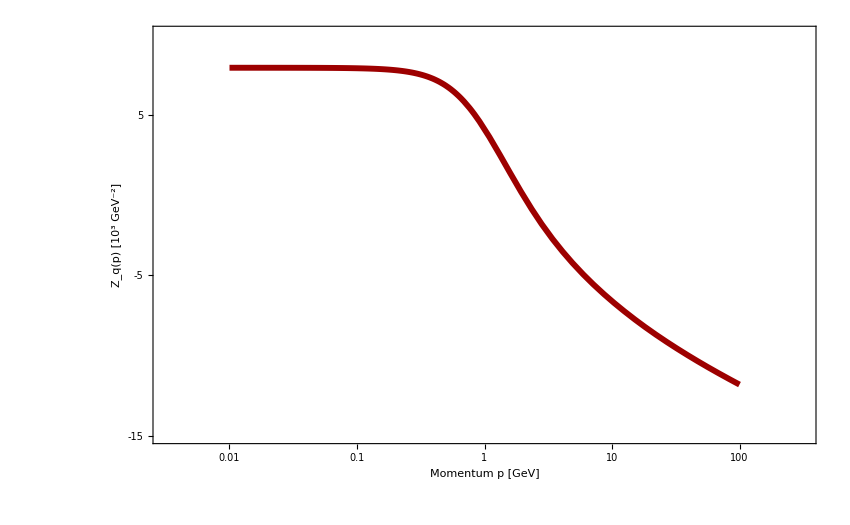

```mathematica
ZqPlot=LogLinearPlot[Interpolation[quarkSEScalItersE[[1]]][p],{p,10^-2,10^2},
ImageSize->850,Frame->True,Exclusions->None,Axes->None,
PlotRange->{xRange={10^-2.5,10^2.5},yRange={-15,10}},
PlotStyle->{Directive[MScRed,Thickness[0.005]]}, 
LabelStyle->MScFont,
FrameStyle->Directive[Black,Thickness[0.005]],
FrameLabel->{"Momentum p [GeV]", "  Z_q(p) [10^3 GeV^-2]"},
FrameTicks->{{LinTicks[Sequence@@yRange, ShowMinorTicks->False,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[Sequence@@xRange,ShowMinorTicks->True,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True,LogPlot->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}}
(*Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
]
exportFigure[ZqPlot];
```

## Comparison Euclidean Propagator - Spectral Representation

## Appendices etc.